## Implementation of the MCA Algorithm for finding the matrix inverse

1) Find the Minors Matrix
2) Find the Cofactors Matrix : Minors Matrix .* CofactorSignsMatrix
3) Find the Adjugate Matrix (the Inverse) : Transpose[CofactorsMatrix] / (Matrix Determinant)

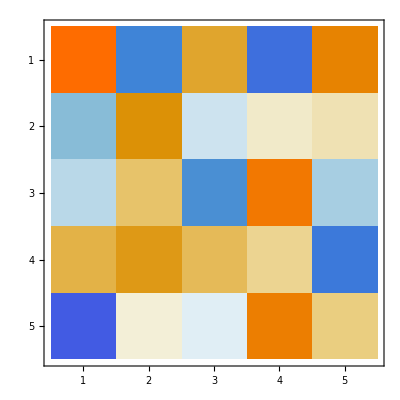
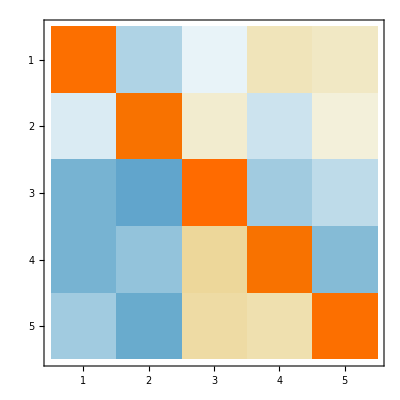

```mathematica
(* Find the Minors Matrix *)
m1Sz = 5;
signMatrixPosVal = 1;
posList = Range[m1Sz];
M1 = RandomReal[5.0, {m1Sz,m1Sz}];
M1Det = Det[M1];
If[Abs[M1Det] > 0,
(* Create a 0's placeholder for the MinorsMatrix *)
MinorsMatrix  = RandomInteger[0, {m1Sz, m1Sz}];
CofactorSignsMatrix = RandomInteger[0, {m1Sz,m1Sz}];

(* Find the determinant of the sub matrix by excluding 
  The row and column of the position being determined *)
For [M1Row = 1, M1Row ≤ m1Sz, M1Row++,
For [M1Col = 1, M1Col ≤ m1Sz, M1Col++,
(* Build the CofactorSignsMatrix *)
CofactorSignsMatrix[[M1Row,M1Col]] = signMatrixPosVal;

(* Flip the sign for the next position *)
signMatrixPosVal = -1 * signMatrixPosVal; 

(* Build the row/column list, exclude the row/col of position being calculated *)
SubMatrix = M1[[Delete[posList,M1Row],Delete[posList,M1Col]]];
SubMatrixDet = Det[SubMatrix];
MinorsMatrix[[M1Row,M1Col]] = SubMatrixDet;
]
];

(* Create the co-factors matrix which is MinorsMatrix * CoFactorsMatrixSignsMatrix *)

(* Hadamard (element wise) multiplication *)
CoFactorsMatrix = MinorsMatrix * CofactorSignsMatrix;

(* The Adjugate Matrix (The Matrix Inverse) *)
AdjugateMatrix = Transpose[CoFactorsMatrix] * 1/M1Det;

(* Test the inverse, should give us the identity matrix when multiplied (Dot, not Hadamard) with the original matrix. Computer rounding means off diagonal values will be near but not exactly 0. *)
MatrixPlot[AdjugateMatrix]
MatrixPlot[Dot[M1,AdjugateMatrix] ]

,(* Nothing to do for the false case *)](* End If Determinant > 0 *)
```